```mathematica
(*CONSTANTS AND SIMPLE FUNCTIONS USED*)

(*Convection*)
cp =29.3; (*J/ mol K*)
wind = 1; (*m/s*)
(*original data tissue density:
1 kg /l =  1 kg/dm^3 = 1000g/dm^3 = 1000 g/ 10^(-3) m^3  = 1 10^6 g/m^3
*)
δ = 10^(6);(* g/m^3*)
Ksth =0.05* cp (*this is tissue conductance. A sleeping bag has 0.05 *);
(*2.092 10 ^(-12)*)  (*5 10^(-7) cal/s C mm2 = 4.184 *5 10^(-7) 10^(-6) W/C m2 *)

s = 3.3472 ;(*specific heat capacity, 0.8 cal /g C = 0.8*4.184 J/g C*)
σ=5.67 10^(-8);(*W/m2 K4*)
e = 0.04184;(*energy per contraction: 0.01 cal/g = 0.01*4.184 j/g*)

Kv[z_]:= cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (* J/mol K x mol /m2 s *);
(*, Conversion: 1 cal = 4.184 J, 1m2 = (1000 mm)^2 = 10^6 mm2 thus 1 mm2 = 10^(-6) m2*)

aw = 0.25; (*something per second*)
f[T_]:= aw T;

(*Start from radius calculating it is easier *)
rad[z_]:= (3. z/(4 π δ))^(1/3);
As[z_]:= 3. π rad[z]^2 (* m2*); (* Total surface area*)
Ath[z_]:= 2. π(rad[z])^2;  (*Thoracic surface area, circle surface =  π r^2, sphere surface = 4 π r^2 *)
```

```mathematica
(*for plotting*)
th = 2; asz =16;
```

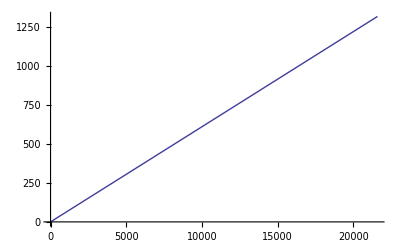

```mathematica
Plot[SR[t],{t,0,6*3600}]
```

```mathematica
SR  = #/(6*3600) * 1320. &;
Te = #2 + 0 #1/(6*3600.) &;
```

```mathematica
(*this function is for the change in thoracic (and surface) temperature *)
changeTth[z_, rK1_, rK2_,minT_,free_]:= Module[{maxt = 6*3600, ε= 0.95, r3 =0.5,sol},
sol = If[free == 0,
NDSolve[
{ Tth'[t] == 1/(s z/2) (0. *z/2 e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05(Ts[t]- Te[t,minT])^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}],
NDSolve[
{Tth'[t] == 1/(s z/2) (0. * z/2 e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Te[t,minT]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}]
];
sol];
```

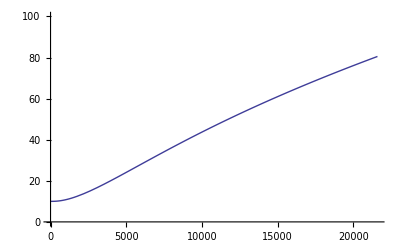

```mathematica
tt =changeTth[0.01,0.5,2,10,0];
Plot[Evaluate[Tth[t]/. tt[[1]]], {t, 0 ,6*3600},PlotRange-> {0,100}]
```

```mathematica
(*This finds an interval of temperature such that at maxt, f(T1) < Tw and f(T2)>Tw, the condition is that Abs[f(t1) - f(t2)] < 0.01*)
findTmin[z_, rK1_, rK2_, free_]:=Module[{Tw = 28 + 0. 0.75 z,T1,T2, Tmid,maxt = 6*3600,Tf1,Tf2,sol,Tfmid},
T1 = 0;
T2 = 100;
Tf1 = 0;
Tf2 = 100; 
Tmid = T1;

sol  = changeTth[z,rK1, rK2, T1, free];
Tf1 = Tth[maxt]/.sol[[1]];
If[Tf1 > Tw, Goto[end]];

While[Abs[Tf1 -Tf2] > 10^(-2),
Tmid = T1 + (T2 - T1 )/2;

sol  = changeTth[z,rK1, rK2, Tmid, free];
Tfmid = Tth[maxt]/.sol[[1]];

Which[
Tfmid < Tw,Tf1 = Tfmid;T1 = Tmid,
Tfmid > Tw,Tf2 = Tfmid;T2 = Tmid,
Tfmid == Tw,T1 = Tmid;Goto[end] 
];
];
Label[end];
N@{z,T1}];
```

```mathematica
vect = Flatten[{Range[0.001,0.01,0.001],Range[0.02,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];
```

```mathematica
DATA= {1,2};
Do[
data= Table[Table[findTmin[z,rK1,rK2,case-1], {z, vect}],{rK1,{0.1,1,10}},{rK2,{0.1,1,10}}];
DATA[[case]] = data;
,{case,{1,2}}];
```

```mathematica
fig = {};
Do[
d1 = ListPlot[DATA[[case,1]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d2 = ListPlot[DATA[[case,2]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d3 = ListPlot[DATA[[case,3]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
AppendTo[fig,{d1,d2,d3}];
,{case,{1,2}}];
```

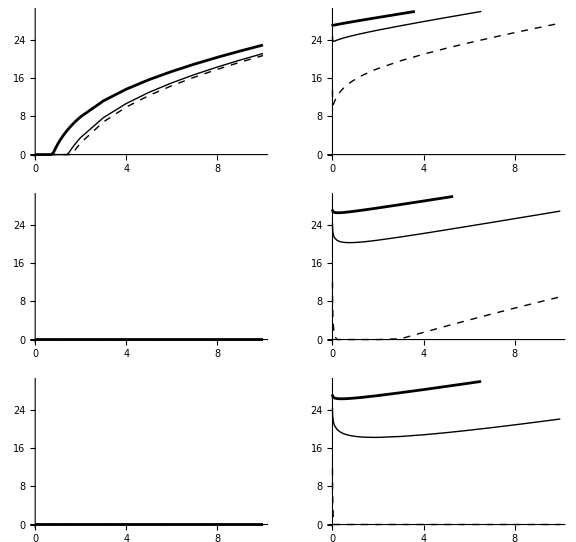

```mathematica
out =GraphicsGrid[Transpose[fig],ImageSize->Large]
```

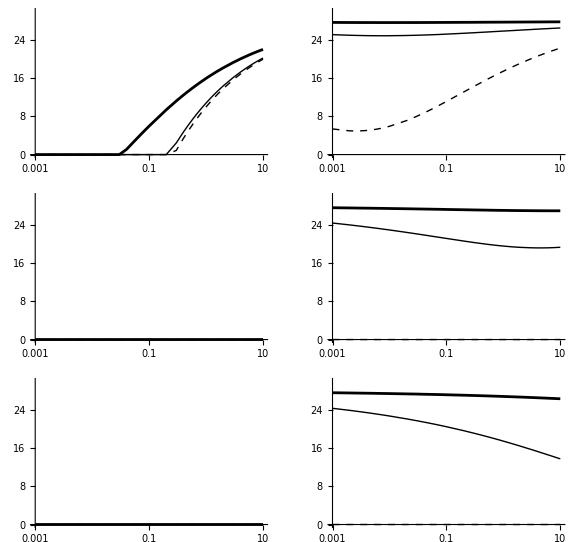

```mathematica
fig = {};
Do[
d1 = ListLogLinearPlot[DATA[[case,1]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d2 = ListLogLinearPlot[DATA[[case,2]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d3 = ListLogLinearPlot[DATA[[case,3]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
AppendTo[fig,{d1,d2,d3}];
,{case,{1,2}}];
out =GraphicsGrid[Transpose[fig],ImageSize->Large]
```